```mathematica
(* Applied Field direction *)
uh={1,0,0};
uk={0,0,1};
(* Shape anisotropy (demag field) *)
Ndemag={{0,0,0},{0,0,0},{0,0,1}};
p={1/Sqrt[2],0,1/Sqrt[2]}; (* vecteur polarization *)
ku2=0;
```

```mathematica
(* Uniaxial anisotropy in J/m3 *)
ku1=102648;
(* Saturation magnetization in A/m *)
Ms= 11.72*10^5;
```

```mathematica
(* Spin transfer torque direction *)

bV [V_]:= 0.03*V^2
b = 0.03;
(* Gilbert damping *)
α=0.01;

(* Constant definitions *)
μ =4*Pi*10^-7;(* free space permeability *)
γ=(2*Pi)*28*10^9;(* gyromagnetic factor rad/sT *)
```

```mathematica
Needs["FourierSeries`"]
Needs["VariationalMethods`"];
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
```

```mathematica
(* magnetization function definition *)
m[θ_,ϕ_]:={Sin[θ]*Cos[ϕ],Sin[θ]*Sin[ϕ],Cos[θ]};  (* aimantation normalisée en coordonnées polaires *)
M[θ_,ϕ_]:=Ms*m[θ,ϕ]; (* aimantation en coordonnées polaires *)

(* definition des énergies ne dépendant pas de H *)
Edem[θ_,ϕ_]:= μ /2*Ms^2*m[θ,ϕ].(Ndemag.m[θ,ϕ]);
Eani[θ_,ϕ_]:=-ku1(uk.m[θ,ϕ])^2-ku2(uk.m[θ,ϕ])^4;

(* definition des énergies dépendant de H et de V*)
Ezeeman[θ_,ϕ_,H_]:= - μ Ms(H/μ)m[θ,ϕ].uh; 

Estt[θ_,ϕ_,V_]:= - μ Ms(bV[V]/μ)m[θ,ϕ].p; 
Etot[θ_,ϕ_,H_,V_]:=Ezeeman[θ,ϕ,H]+Estt[θ,ϕ,V]+Eani[θ,ϕ]+Edem[θ,ϕ];
(* definition du Lagrangien *)
ℒ[t_,H_,V_]:=-Ms/γ*D[ϕ[t],t]*Cos[θ[t]]-Etot[θ[t],ϕ[t],H,V];

(* Damping fonction de Rayleigh *)
ℱdamping[D[θ[t],t],D[ϕ[t],t]]=α*Ms/(2γ)*(Dt[m[θ[t],ϕ[t]],t].Dt[m[θ[t],ϕ[t]],t])//FullSimplify;
```

```mathematica
Condition initiales
```

```mathematica
(* Max time calculation *)
tmax=40 10^-9;(* in s*)

Print[x];
V= -0.6;(* Initial position *)
H =0.05;(*T*)
(*V=0.1;*)(*V*)
{θi,ϕi}={1,Pi/2}; 
(* direction initiale de l'aimantation dans la base canonique *)

(* Spin transfer torque *)
aV=0.008*V; (* Slonc Torque for MTJ avec aV/V en  *)
(*Print[aV];*)
(* Rayleigh's dissipaµtion functions : régférence http://www.academia.edu/4733940/Spin_transfer_and_current-induced_switching_in_antiferromagnets, soit *)
ℱslonc[D[θ[t],t],D[ϕ[t],t]]=Ms*aV*p.(m[θ[t],ϕ[t]]×Dt[m[θ[t],ϕ[t]],t])//FullSimplify;
(* reférence bibliographique : Lagrangian formulation of the linear autonomous magnetization
dynamics in spin-torque auto-oscillators, G.Consolo,G.Gubbiotti,L.Giovannini,R.Zivieri, Applied Mathematics and Computation 217 (2011) 8204–8215 *)

dℱθ=D[(ℱdamping[D[θ[t],t],D[ϕ[t],t]]+ℱslonc[D[θ[t],t],D[ϕ[t],t]]),D[θ[t],t]];
dℱϕ=D[(ℱdamping[D[θ[t],t],D[ϕ[t],t]]+ℱslonc[D[θ[t],t],D[ϕ[t],t]]),D[ϕ[t],t]];

(* full numericall LLG and time evolution evaluation *)
LLGwithoutdamping=EulerEquations[ℒ[t,H,V],{θ[t],ϕ[t]},t];
System={LLGwithoutdamping[[1]]//.0-> dℱθ,LLGwithoutdamping[[2]]//.0-> dℱϕ};
Evol=NDSolve [Flatten[{System,θ[0]==θi,ϕ[0]==ϕi}],{θ,ϕ},{t,0,tmax},Method->Automatic, StartingStepSize->10^-15];
θcalc[t_]:=Evaluate[θ[t]/.Evol][[1]];
ϕcalc[t_]:=Evaluate[ϕ[t]/.Evol][[1]];
Show[{ParametricPlot3D[{{m[θcalc[t],ϕcalc[t]]}},{t,0,tmax},PlotStyle->{Black,Thin},Axes->False,Boxed->False],
ParametricPlot3D[{Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]},{u,0,2π},{v,0,π},PlotStyle-> None,PerformanceGoal->"Quality",Mesh->12,MeshStyle->Directive[{Gray,Thin,Dotted}],Boxed->False,Axes->None],Graphics3D[{RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098], Sphere[m[θcalc[tmax],ϕcalc[tmax]],0.03],RGBColor[0.6313725490196078, 0.6313725490196078, 0.24705882352941178], Sphere[m[θcalc[0],ϕcalc[0]],0.03],Black,Thin,Dashed,Arrow[{{0,0,-1},{0,0,1.2}}],Arrow[{{0,-1,0},{0,1.2,0}}],Arrow[{{-1,0,0},{1.2,0,0}}]}]},PlotRange->All]


(*
Print[Show[{ParametricPlot3D[{{m[θcalc[t],ϕcalc[t]]},{m[θi,2Pi *t/tmax]}},{t,0,tmax},PlotStyle->{Red,Blue},AxesLabel->{mx,my,mz}],Graphics3D[{Opacity[0.3],Gray,Sphere[{0,0,0}],Black,Thick,Line[{{0,0,0},m[θcalc[tmax],ϕcalc[tmax]]}]}]},PlotRange->All]];*)(*


Print[Plot[θcalc[t],{t,0,tmax},PlotRange->All]];
Print[Plot[ϕcalc[t],{t,0,tmax}]];*)
```

x

-Graphics3D-

```mathematica
SetDirectory["C:\\Users\\Marion\\Documents\\RedactionThese\\Energy"];
```

```mathematica
Export["TrajTiltAniHm150mTVm750mV.png",%]
```

```mathematica
ϕcalc[t]
```

-8
InterpolatingFunction[{{0., 4. 10  }}, <>][t]

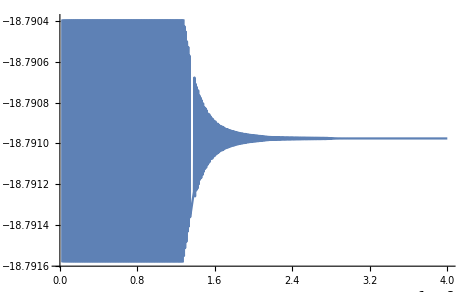

```mathematica
Plot[%333,{t,0.,4.*^-8}]
```

```mathematica
D[ϕcalc[t],t]
```

-8
InterpolatingFunction[{{0., 4. 10  }}, <>][t]

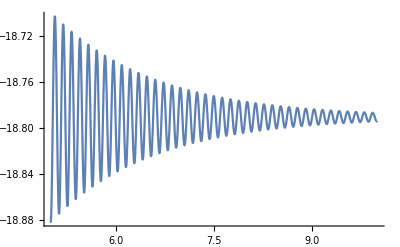

```mathematica
Plot[ϕcalc[t],{t,0.5×10^-8,1×10^-8}]
```

```mathematica
(*Plot[NFourierTransform[ϕcalc[t],t,ω],{ω,0,1×10^8},PlotRange->All]*)
```

InterpolatingFunction::dmval: Input value {-0.000538975} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.00130175} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.00245713} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NIntegrate::deorel: The relative error 1.00147 is larger than expected for the integrand « 1 » over {0, ∞} with DoubleExponentialOscillatory method and tuning parameters, TuningParameters -> {10, 5}.

NIntegrate::deoncon: DoubleExponentialOscillatory has failed to converge for the integrand « 1 » over {0, ∞}. DoubleExponentialOscillatory obtained -7.60489×10^27 and 10.0147 for the integral and error estimates.

NIntegrate::inumr: The integrand « 1 » has evaluated to non-numerical values for all sampling points in the region with boundaries {{0., -42.4925}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::deorel: The relative error 1.00147 is larger than expected for the integrand « 1 » over {0, ∞} with DoubleExponentialOscillatory method and tuning parameters, TuningParameters -> {10, 5}.

NIntegrate::deoncon: DoubleExponentialOscillatory has failed to converge for the integrand « 1 » over {0, ∞}. DoubleExponentialOscillatory obtained -7.60489×10^27 and 10.0147 for the integral and error estimates.

NIntegrate::inumrexpr: Expression TagBox[InterpolatingFunction[{{0.`, 4.`*^-8}}, {5, 7, 1, {4992}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{« 1 »}}, {Developer`PackedArrayForm, {0, « 50 »}, {1.5707963267948966`, -1.2139362806387213`*^11, 1.5706749307243455`, -1.2139607055099042`*^11, 1.570553532211257`, -1.2139851308856871`*^11, 1.5590307962063685`, -1.2163035012002667`*^11, 1.5474860560373547`, -1.2186260833391704`*^11, 1.5359192733140428`, « 29 », 0.4477345103699093`, -1.393352927399876`*^11, 0.32184716506150557`, -1.4020669731154486`*^11, 0.19531761540734544`, -1.4075798989564343`*^11, 0.06844293664270694`, -1.409707849278615`*^11, -0.05846675205486906`, -1.408347166450516`*^11, « 9934 »}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]][t] derived from integrand 2.718281828459045 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-12024.9, -31.0854}}.

NIntegrate::mtdfb: Numerical integration with "LevinRule" failed. The integration continues with Method -> "GaussKronrodRule".

NIntegrate::inumrexpr: Expression TagBox[InterpolatingFunction[{{0.`, 4.`*^-8}}, {5, 7, 1, {4992}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{« 1 »}}, {Developer`PackedArrayForm, {0, « 50 »}, {1.5707963267948966`, -1.2139362806387213`*^11, 1.5706749307243455`, -1.2139607055099042`*^11, 1.570553532211257`, -1.2139851308856871`*^11, 1.5590307962063685`, -1.2163035012002667`*^11, 1.5474860560373547`, -1.2186260833391704`*^11, 1.5359192733140428`, « 29 », 0.4477345103699093`, -1.393352927399876`*^11, 0.32184716506150557`, -1.4020669731154486`*^11, 0.19531761540734544`, -1.4075798989564343`*^11, 0.06844293664270694`, -1.409707849278615`*^11, -0.05846675205486906`, -1.408347166450516`*^11, « 9934 »}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]][t] derived from integrand 2.718281828459045 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-12024.9, -31.0854}}.

NIntegrate::mtdfb: Numerical integration with "LevinRule" failed. The integration continues with Method -> "GaussKronrodRule".

NIntegrate::deorela: The relative error 3.47579 is larger than expected for the integrand « 1 » over {0, ∞} with DoubleExponentialOscillatory method and automatic tuning parameters, TuningParameters -> {10, 5}. The integration will proceed with TuningParameters -> {1, 5}.

InterpolatingFunction::dprec: The precision of input value {-16.} and/or the interpolation grid is insufficient to compute the value.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::deorela: The relative error 3.47579 is larger than expected for the integrand « 1 » over {0, ∞} with DoubleExponentialOscillatory method and automatic tuning parameters, TuningParameters -> {10, 5}. The integration will proceed with TuningParameters -> {1, 5}.

InterpolatingFunction::dprec: The precision of input value {-16.} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction :: dprec will be suppressed during this calculation.

NIntegrate::inumrexpr: Expression TagBox[InterpolatingFunction[{{0.`, 4.`*^-8}}, {5, 7, 1, {4992}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{« 1 »}}, {Developer`PackedArrayForm, {0, « 50 »}, {1.5707963267948966`, -1.2139362806387213`*^11, 1.5706749307243455`, -1.2139607055099042`*^11, 1.570553532211257`, -1.2139851308856871`*^11, 1.5590307962063685`, -1.2163035012002667`*^11, 1.5474860560373547`, -1.2186260833391704`*^11, 1.5359192733140428`, « 29 », 0.4477345103699093`, -1.393352927399876`*^11, 0.32184716506150557`, -1.4020669731154486`*^11, 0.19531761540734544`, -1.4075798989564343`*^11, 0.06844293664270694`, -1.409707849278615`*^11, -0.05846675205486906`, -1.408347166450516`*^11, « 9934 »}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]][t] derived from integrand 2.718281828459045 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-12024.9, -31.0854}}.

General::stop: Further output of NIntegrate :: inumrexpr will be suppressed during this calculation.

NIntegrate::mtdfb: Numerical integration with "LevinRule" failed. The integration continues with Method -> "GaussKronrodRule".

General::stop: Further output of NIntegrate :: mtdfb will be suppressed during this calculation.

NIntegrate::deorel: The relative error 2.04526 is larger than expected for the integrand « 1 » over {0, ∞} with DoubleExponentialOscillatory method and tuning parameters, TuningParameters -> {10, 5}.

General::stop: Further output of NIntegrate :: deorel will be suppressed during this calculation.

NIntegrate::deoncon: DoubleExponentialOscillatory has failed to converge for the integrand « 1 » over {0, ∞}. DoubleExponentialOscillatory obtained 1.76223×10^11 and 20.4526 for the integral and error estimates.

General::stop: Further output of NIntegrate :: deoncon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-14.0623}. NIntegrate obtained 3.28511×10^43 and 8.98509×10^43 for the integral and error estimates.

NIntegrate::deorela: The relative error 7.22078 is larger than expected for the integrand (0.`  - 1.` ⅈ) over {0, ∞} with DoubleExponentialOscillatory method and automatic tuning parameters, TuningParameters -> {10, 5}. The integration will proceed with TuningParameters -> {1, 5}.

General::stop: Further output of NIntegrate :: deorela will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-14.0623}. NIntegrate obtained 3.28511×10^43 and 8.98509×10^43 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-12.1309}. NIntegrate obtained -4.33126×10^43 and 4.34435×10^43 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::deodiv: DoubleExponentialOscillatory returns a finite integral estimate, but the integral might be divergent.

General::stop: Further output of NIntegrate :: deodiv will be suppressed during this calculation.

```mathematica
NFourierTransform[Piecewise[{{ϕcalc[t],0<t<10^-8}},0],t,dw,Method->{"GlobalAdaptive",Method->"LevinRule","SymbolicProcessing"->0}]
```

NFourierTransform[Piecewise[{{-8
InterpolatingFunction[{{0., 4. 10  }}, <>][t], 0<t<1/100000000}, {0, True}}],t,dw,Method→{GlobalAdaptive,Method→LevinRule,SymbolicProcessing→0}]

```mathematica
NFourierTransform[ϕcalc[t],t,1.*^-8]
```

InterpolatingFunction::dmval: Input value {-1.10105×10^8} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-1.10105×10^8} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-1.10105×10^8} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-1.10105×10^8} and/or the interpolation grid is insufficient to compute the value.

NIntegrate::inumr: The integrand « 1 » has evaluated to non-numerical values for all sampling points in the region with boundaries {{0., -42.4925}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-1.10105×10^8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {-1.10105×10^8} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction :: dprec will be suppressed during this calculation.

NIntegrate[ⅇ^((0.+1.×10^-8 ⅈ) t)                                  -8
InterpolatingFunction[{{0., 4. 10  }}, <>][t],{t,-∞,∞}]/(√(2 π))

```mathematica
∂_t %327
```

-8
InterpolatingFunction[{{0., 4. 10  }}, <>][t]

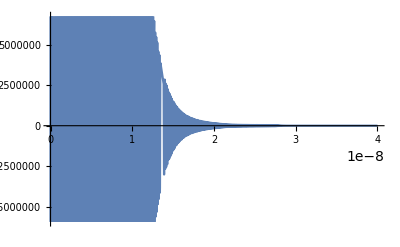

```mathematica
Plot[%328,{t,0.,4.*^-8}]
```

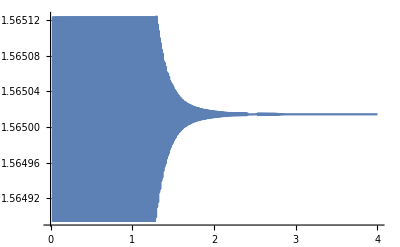

```mathematica
Plot[%319,{t,0.,4.*^-8}]
```

```mathematica
D[θcalc[t],t]
```

-8
InterpolatingFunction[{{0., 4. 10  }}, <>][t]

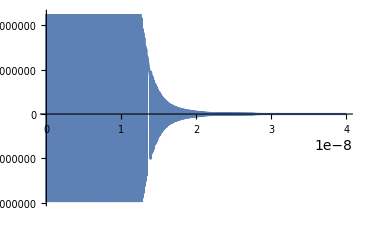

```mathematica
Plot[%321,{t,0.,4.*^-8}]
```

```mathematica
ListLinePlot[Abs[Fourier[θcalc]],PlotRange->All]
```

Fourier::fftl: Argument θcalc is not a non-empty list or rectangular array of numeric quantities.

ListLinePlot::lpn: Abs[Fourier[θcalc]] is not a list of numbers or pairs of numbers.

```mathematica
ListLinePlot[Abs[Fourier[θcalc[t]]],{t,0.,4.*^-8}]
```

Fourier::fftl: Argument TagBox[InterpolatingFunction[{{0.`, 4.`*^-8}}, {5, 7, 1, {4992}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{« 1 »}}, {Developer`PackedArrayForm, {« 1 »}, {1.`, -8.616033001247559`*^9, 0.9999913839400288`, -8.6160599710639`*^9, 0.9999827678532356`, -8.616086793221949`*^9, 0.999165649484461`, -8.617957984503073`*^9, 0.9983484170078335`, -8.618493470050549`*^9, 0.9975311974519393`, -8.617685470137827`*^9, « 27 », -4.0209498445256786`*^9, 0.9417975719176506`, -3.0969959867308884`*^9, 0.9395297309770323`, -1.9278751428886752`*^9, 0.9383439441783551`, -6.972583735690454`*^8, 0.9382858691319592`, 5.729570499681802`*^8, 0.9393807363042644`, 1.8594431719016697`*^9, « 9934 »}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]] is not a non-empty list or rectangular array of numeric quantities.

ListLinePlot::nonopt: Options expected (instead of {t, 0., 4.×10^-8}) beyond position 1 in Abs[Fourier[TagBox[InterpolatingFunction[{{0.`, 4.`*^-8}}, {5, 7, 1, {4992}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, {« 1 »}, {Developer`PackedArrayForm, {0, 2, 4, « 45 », 96, 98, « 4943 »}, {1.`, -8.616033001247559`*^9, 0.9999913839400288`, -8.6160599710639`*^9, 0.9999827678532356`, -8.616086793221949`*^9, 0.999165649484461`, -8.617957984503073`*^9, 0.9983484170078335`, -8.618493470050549`*^9, 0.9975311974519393`, « 29 », 0.9417975719176506`, -3.0969959867308884`*^9, 0.9395297309770323`, -1.9278751428886752`*^9, 0.9383439441783551`, -6.972583735690454`*^8, 0.9382858691319592`, 5.729570499681802`*^8, 0.9393807363042644`, 1.8594431719016697`*^9, « 9934 »}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]][t]]], « 1 ». An option must be a rule or a list of rules.

ListLinePlot[Abs[Fourier[                                 -8
InterpolatingFunction[{{0., 4. 10  }}, <>][t]]],{t,0.,4.×10^-8}]

```mathematica
Plot[θcalc[t],{t,0.,4.*^-8},Epilog->Point[points]]
```

-Graphics-

```mathematica
θcalc[1.*^-8]
```

1.56534

```mathematica
Fourier[θcalc,FourierParameters->{-1, 1}]
```

Fourier::fftl: Argument θcalc is not a non-empty list or rectangular array of numeric quantities.

Fourier[θcalc,FourierParameters→{-1,1}]

```mathematica
list1= Range[1.*^-8,2.*^-8,1.*^-12]
```

{1.×10^-8,1.0001×10^-8,1.0002×10^-8,1.0003×10^-8,1.0004×10^-8,1.0005×10^-8,1.0006×10^-8,1.0007×10^-8,1.0008×10^-8,1.0009×10^-8,1.001×10^-8,1.0011×10^-8,1.0012×10^-8,1.0013×10^-8,1.0014×10^-8,1.0015×10^-8,1.0016×10^-8,1.0017×10^-8,1.0018×10^-8,1.0019×10^-8,1.002×10^-8,9959,1.998×10^-8,1.9981×10^-8,1.9982×10^-8,1.9983×10^-8,1.9984×10^-8,1.9985×10^-8,1.9986×10^-8,1.9987×10^-8,1.9988×10^-8,1.9989×10^-8,1.999×10^-8,1.9991×10^-8,1.9992×10^-8,1.9993×10^-8,1.9994×10^-8,1.9995×10^-8,1.9996×10^-8,1.9997×10^-8,1.9998×10^-8,1.9999×10^-8,2.×10^-8}
 |  |  |  |

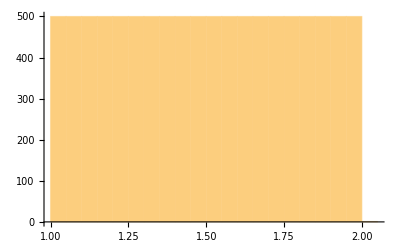

```mathematica
Histogram[list1]
```

```mathematica
m=θcalc[list1]
```

{1.56534,1.56537,1.56541,1.56544,1.56547,1.56549,1.56552,1.56555,1.56557,1.5656,1.56562,1.56564,1.56566,1.56568,1.56569,9971,1.56502,1.56502,1.56502,1.56502,1.56502,1.56502,1.56502,1.56502,1.56502,1.56502,1.56502,1.56502,1.56502,1.56502,1.56502}
 |  |  |  |

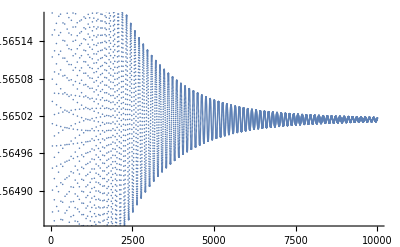

```mathematica
ListPlot[m]
```

```mathematica
mF=Fourier[m,FourierParameters->{-1,1}]
```

{1.56502-1.17228×10^-17 ⅈ,1.39865×10^-6-8.50509×10^-9 ⅈ,1.40251×10^-6-1.57652×10^-8 ⅈ,1.40385×10^-6-2.43801×10^-8 ⅈ,1.40372×10^-6-3.09598×10^-8 ⅈ,1.40564×10^-6-4.00319×10^-8 ⅈ,9989,1.40717×10^-6+4.80878×10^-8 ⅈ,1.40564×10^-6+4.00319×10^-8 ⅈ,1.40372×10^-6+3.09598×10^-8 ⅈ,1.40385×10^-6+2.43801×10^-8 ⅈ,1.40251×10^-6+1.57652×10^-8 ⅈ,1.39865×10^-6+8.50509×10^-9 ⅈ}
 |  |  |  |

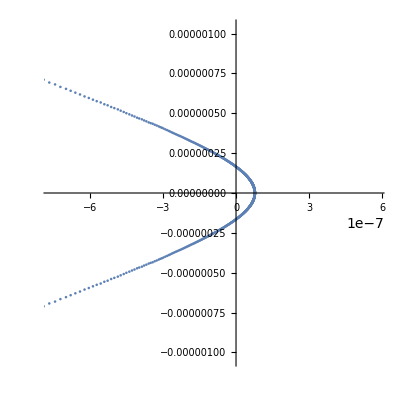

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@mF,AspectRatio->1]
```

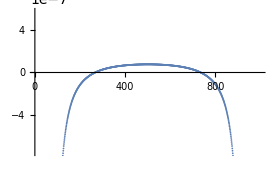

-Graphics-

```mathematica
ListPlot[%47]
```

```mathematica
mF2=PeriodogramArray[m]
```

{24495.2,1.95649×10^-8,1.96748×10^-8,1.97159×10^-8,1.97158×10^-8,1.97762×10^-8,1.98264×10^-8,1.99708×10^-8,2.0122×10^-8,2.0232×10^-8,2.03887×10^-8,2.05419×10^-8,2.06994×10^-8,9975,2.09227×10^-8,2.06994×10^-8,2.05419×10^-8,2.03887×10^-8,2.0232×10^-8,2.0122×10^-8,1.99708×10^-8,1.98264×10^-8,1.97762×10^-8,1.97158×10^-8,1.97159×10^-8,1.96748×10^-8,1.95649×10^-8}
 |  |  |  |

```mathematica
mF3=Drop[mF2,1]
```

{1.95649×10^-8,1.96748×10^-8,1.97159×10^-8,1.97158×10^-8,1.97762×10^-8,1.98264×10^-8,1.99708×10^-8,2.0122×10^-8,2.0232×10^-8,2.03887×10^-8,2.05419×10^-8,2.06994×10^-8,2.09227×10^-8,9974,2.09227×10^-8,2.06994×10^-8,2.05419×10^-8,2.03887×10^-8,2.0232×10^-8,2.0122×10^-8,1.99708×10^-8,1.98264×10^-8,1.97762×10^-8,1.97158×10^-8,1.97159×10^-8,1.96748×10^-8,1.95649×10^-8}
 |  |  |  |

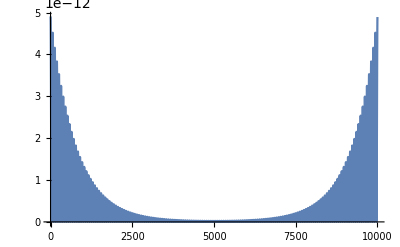

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

```mathematica
ListLinePlot[PeriodogramArray[Drop[mF2,1]],PlotRange->All]
```

```mathematica
data=Table[{t,Sin[2 Pi 697 t]+Sin[2 Pi 1209 t]},{t,0.,0.1,1/8000.}];
```

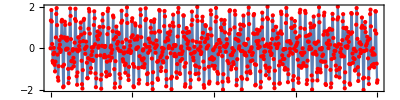

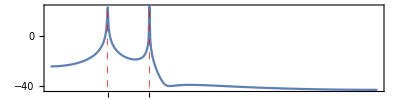

```mathematica
ListLinePlot[data,AspectRatio->1/4,Mesh->All,MeshStyle->Directive[PointSize[Small],Red],Frame->True]

Periodogram[data[[All,2]],SampleRate->8000,Frame->True,GridLines->{{697,1209},None},FrameTicks->{{All,All},{{697,1209},All}},GridLinesStyle->Directive[Red,Dashed],AspectRatio->1/4]
```

```mathematica
dataF=   Table[{t,θcalc[t]},  {t,0.*^-9,1.*^-8,1.*^-12}]
```

{{0.,1.},{1.×10^-12,0.991395},{2.×10^-12,0.982916},{3.×10^-12,0.974722},{4.×10^-12,0.966976},{5.×10^-12,0.959844},{6.×10^-12,0.953487},{7.×10^-12,0.94806},{8.×10^-12,0.943704},{9.×10^-12,0.940543},9982,{9.992×10^-9,1.56506},{9.993×10^-9,1.56509},{9.994×10^-9,1.56513},{9.995×10^-9,1.56517},{9.996×10^-9,1.5652},{9.997×10^-9,1.56524},{9.998×10^-9,1.56527},{9.999×10^-9,1.56531},{1.×10^-8,1.56534}}
 |  |  |  |

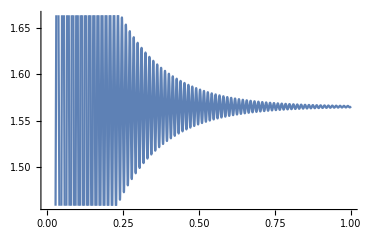

```mathematica
ListPlot[dataF,Joined->True]
```

```mathematica
ArrayPlot[dataF]
```

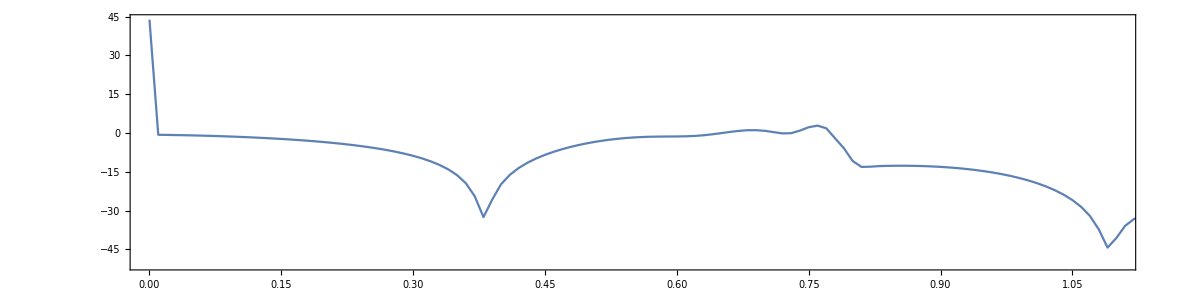

```mathematica
Periodogram[dataF[[All,2]],SampleRate->1.*^12,Frame->True,GridLinesStyle->Directive[Red,Dashed],AspectRatio->1/4,PlotRange->{{0,1.1*^10},All}]
```

```mathematica
len= Length@dataF;
time= 1.*^-8;
```

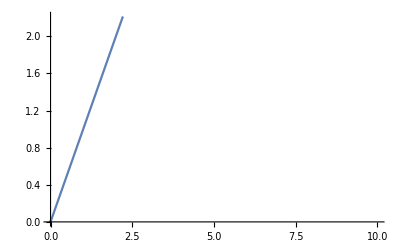

```mathematica
ListLinePlot[Sqrt[4/len] Abs@Fourier[dataF],PlotRange->{{0,1.*^1},All},DataRange->{0,(len-1)/time}]
```